```mathematica
(******************   ENERGY OPTIMIZATION OF EXOTIC HARMONIUM MODEL    *****************)
(* The following codes try to minimize the variational energy of exotic harmonium model and obtain optimized variational parameters (here a and b). Also, calculating the energy using finite element method, hessian and gradient ensures that the best parameters have been obtained. *)
(* Trial Wave function: ψ=e^(-ar-br^2)  Potential: V=-1/r+1/2*μω^2 r^2 *)


(* Inputs of system in a.u. *)
me=1;
mp=1;
μ=(me*mp)/(me+mp);
ω=0.0001;

(* Input of FEM *)
rMin=10^-16;
rMax=50.;
n=20;
meshDisc=0.001;

(* Input of Variation Method *)
step=0.001;
conv=7;

initialParam={0.9090909020621444,1.1754907046612933*^-8};
rMinNI=0.;
rMaXNI=∞;
```

### Mean Field Converged ###

μ                  = 1/2

ω                  = 0.0001

Finale step        = 1.×10^-8

Finale Status List = {fixed,fixed}

Optimized point    = {0.5,1.17549×10^-8}

Optimized Energy   = -0.25

| a | b | ω | μ | Variational Energy | Numerical Energy | Delta E | RMSD
 | 0.5 | 1.17549×10^-8 | 0.0001 | 1/2 | -0.25 | -0.25 | -1.46652×10^-10 | 2.40107×10^-9

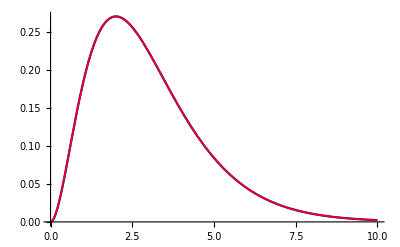

```mathematica
(******************   FINITE ELEMENT METHOD    *****************)
V[r_]:=-1/r+1/2*μ*ω^2*r^2;
eqn=-(1/(2μ)) Laplacian[f[r],{r}] + V[r] *f[r];

{vals,funs}= NDEigensystem[{eqn,DirichletCondition[f[r]==0., r≤rMin],DirichletCondition[f[r]==0., r≥rMax]},f[r],{r,rMin,rMax},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->meshDisc}}}}] ;
ns=Position[vals,Min[vals]][[1,1]];
Er=vals[[ns]];
fr=funs[[ns]];

(******************   VARIATION METHOD    *****************)
(* Variational Integrals *)

int[a_,b_,k_]:=NIntegrate[ r^k Exp[-2*a *r-2*b *r^2],{r,rMinNI,rMaXNI}];
s[a_,b_]:=int[a,b,2];
kin[a_,b_]:=-1/(2μ)(a^2 *int[a,b,2]-2* b *int[a,b,2]+4 *a *b* int[a,b,3]+4 *b^2*int[a,b,4]-2*a*int[a,b,1]-4* b *int[a,b,2]);
pot[a_,b_]:=- int[a,b,1]+1/2*μ*ω^2*int[a,b,4];

w[a_,b_]:=(kin[a,b]+pot[a,b])/s[a,b];


(******************   OPTIMIZATION ALGORITHM     *****************)
(* Initial parameters *)
var=2;
coeff=initialParam;

optStatus=iterating;
list=Array[changed&,var];

i=1;
(* External loop *)
While[optStatus==iterating,

(* plus and minus points *)
minusp=coeff[[i]]-step;
If[minusp<0.,minusp=coeff[[i]]];
plusp= coeff[[i]]+step;

minuscoeff=ReplacePart[coeff,i->minusp];
pluscoeff=ReplacePart[coeff,i->plusp];

(* plus and minus energies *)
w0=w@@coeff;
wMinus=w@@minuscoeff;
wPlus=w@@pluscoeff;

If[wMinus<w0,direction=-step;j=2;wJ[1]=wMinus;
,
If[wPlus<w0,
direction=+step;j=2;wJ[1]=wPlus;
,
list=ReplacePart[list,i->fixed];
i=i+1;
Goto["checkpoint"];

];
];

(* Internal loops *)
Label["StartInnerLoop"];
tempParam=coeff[[i]]+j*direction;
If[tempParam<0.,tempParam=coeff[[i]]];
newcoeff=ReplacePart[coeff,i->tempParam];

wJ[j]=w@@newcoeff;


If[wJ[j]<wJ[j-1],j=j+1;Goto["StartInnerLoop"],

list=ReplacePart[list,i->changed];

coeff=ReplacePart[coeff,i->coeff[[i]]+(j-1)*direction];
i=i+1;
];
(* End of Internal loops *)


Label["checkpoint"];
(*Print["we are in checkpoint"];*)

If[i>var,
If[MemberQ[list,changed]===False,
If[Abs[step]<10.0^-conv,optStatus=finished;Break[]];
step=0.1*Abs[step];i=1;list=Array[changed&,var];
 
,

i=1;
];

];

];
(* Optimized point reached *)
Print[" ### Mean Field Converged ###"];
Print["μ                  = ",μ];
Print["ω                  = ",ω];
Print["Finale step        = ",step];
Print["Finale Status List = ",list];
Print["Optimized point    = ",coeff];
Print["Optimized Energy   = ",w@@coeff];

(* Done with Optimization *)
{a,b}=coeff;


(* RMSD *)
normf[a_,b_]:=(s[a,b])^(-1/2);
fun=normf[a,b]*Exp[-a *r-b *r^2];

sfr=NIntegrate[fr^2,{r,rMin,rMax}];
normfr=sfr^(-1/2);
fr1=normfr*fr;

nrmsd=(rMax-rMin)/10^-3;
rmsd=Sqrt[1/nrmsd Sum[(r r fun^2-fr^2)^2,{r,rMin,rMax,10^-3}]];

deltaE=Er-w[a,b];


(******************   RESULTS     *****************)
chardata=TableForm[{{a,b,ω,μ,w[a,b],Er,deltaE,rmsd}},TableHeadings->{{},{"a","b","ω","μ","Variational Energy","Numerical Energy","Delta E","RMSD"}}]



Plot[{r r fun^2,fr^2},{r,rMin,10},PlotRange->All,PlotStyle->{Blue,{Red,Thickness[.003]}}]
```

```mathematica
Export["chardata.xls",chardata]
```

chardata.xls

```mathematica
(************************     BFGS     ***********************)
VAR[{aa_,bb_},GradientStatus_]:=VAR[{aa,bb},GradientStatus]=Module[{a=aa,b=bb,VARGradientMatrix,VirialRatio,GradMag},

int[a_,b_,k_]:=NIntegrate[ r^k Exp[-2*a *r-2*b *r^2],{r,rMinNI,rMaXNI}];
s[a_,b_]:=int[a,b,2];
kin[a_,b_]:=-1/(2μ)(a^2 *int[a,b,2]-2* b *int[a,b,2]+4 *a *b* int[a,b,3]+4 *b^2*int[a,b,4]-2*a*int[a,b,1]-4* b *int[a,b,2]);
pot[a_,b_]:=- int[a,b,1]+1/2*μ*ω^2*int[a,b,4];

w[a,b]=(kin[a,b]+pot[a,b])/s[a,b];
eng=w[a,b];
(* d/da *)
kina[a_,b_]:=-1/(2μ)(-2 *int[a,b,1]+6 *a *int[a,b,2]-2 *a^2 *int[a,b,3]+16* b *int[a,b,3]-8* a* b *int[a,b,4]-8* b^2 *int[a,b,5]);
pota[a_,b_]:=2 *int[a,b,2]-μ *ω^2*int[a,b,5];
fa[a_,b_]:=-2 *int[a,b,3];


(* d/db *)
kinb[a_,b_]:=-1/(2μ)(-6 *int[a,b,2]+8 *a*int[a,b,3]-2* a^2 *int[a,b,4]+20* b*int[a,b,4]-8* a* b *int[a,b,5]-8 *b^2 *int[a,b,6]);
potb[a_,b_]:=2 *int[a,b,3]-μ* ω^2*int[a,b,6];
fb[a_,b_]:=-2 *int[a,b,4];


(* Gradient *)
If[GradientStatus===grad,
ga=((kina[a,b]+pota[a,b])-w[a,b]*fa[a,b])/s[a,b];
gb=((kinb[a,b]+potb[a,b])-w[a,b]*fb[a,b])/s[a,b];
];
VARGradientMatrix=List[ga,gb];
GradMag=Norm[VARGradientMatrix];

(******************   VIRIAL RATIO     *****************)
rdelV=int[a,b,1]+μ*ω^2*int[a,b,4];
VR=(2 kin[a,b])/rdelV; 

Clear[int,kin,pot,w,kina,kinb,pota,potb,fa,fb,ga,gb,s];
ClearSystemCache[];
Return[{SetPrecision[eng,20],VARGradientMatrix,GradMag,PaddedForm[VR,{9,8}]}]
];
VAR[{0.5000000020621443,1.1754907046612933*^-8},grad]
```

{-0.24999997000000609426,{2.5183×10^-8,7.31207×10^-8},7.73357×10^-8, 1.00000003}

```mathematica
(* BFGS - Trust-region based on double dogleg step calculation *)

(* reference: "Numerical Methods for Unconstrained Optimization and Nonlinear Equations", 
 R.B. Schnabel, SIAM's Classics in Applied Mathematics series,Vol.16, pages 139-143, 1996 *)

(* STEP 0  *)

(* Select an initial point X[0] and a guess for first HESSIAN 
   matrix. Set i=0. Select η1 ∈ (0,η2) and η2 ∈ (η1,1). Compute
 Gradient matrix at X[0]. Select IMAX(maximum number of iterations). 
Select Δ[0](initial trast-region radius) and convergence toleranc 
 ϵ > 0 *)


X0={0.5000000020621443,1.1754907046612933*^-8};


(* STEP 0  *)
ϵ=10^-7;
IMAX=200;
X[0]=Flatten[X0];
Δ[0]=0.001;
η1=0;
η2=0.8;
i=0;
VAROutput[0]=VAR[X[0],grad];
GradientMatrix[0]=VAROutput[0][[2]];
GraMag[0]=VAROutput[0][[3]];
Hess[0]=IdentityMatrix[Length[X[0]]];
(* Outer termination test *)
If[GraMag[0]<ϵ,Print["Initial point is the OPTIMUM point"]];
```

Initial point is the OPTIMUM point

```mathematica
(* Exponents negativity test *)
(* Inputs : two lists, A the current point (i-th point) and B the next point *)
(* This module compares two lists and if there is a negative component
in B-list then it will replace by corresponding positive component
from A-list *)
NegativeTest[A_,B_]:=Module[{firstlist=A,secondlist=B,finalelist,n,i},
n=Length[firstlist];
For[ i=1,i≤n,i++,If[Positive[secondlist][[i]]===True,
finalelist[i]=secondlist[[i]],finalelist[i]=firstlist[[i]]
]];
finalelist=Table[finalelist[i],{i,1,n}];
Return[finalelist];
];
```

```mathematica
(* Set Optimization State to iterating for executing outer loop of optimization *)
OptimizationState=iterating;

(* Start point of outer optimization loops *)

While[OptimizationState==iterating,

(* STEP  1 *)
(* Computing euclidean norm of gradient matrix for cauchy step calculation *)

NormGrad[i]=Norm[GradientMatrix[i]];

(* Computing Quasi-Newton direction vector and store it in "QNdirection" *)

QNdirection[i]=-Inverse[Hess[i]].GradientMatrix[i];

(* Double dogleg Step calculation procedure  *)

(* If euclidean norm of Quasi-Newton vector is less or equal i-th trust-region
  radius, it is our direction vector and no double dogleg step calculation will
   occure   *)

If[Norm[QNdirection[i]]≤Δ[i],hDirection[i]=QNdirection[i];,

(* CAUCHY STEP (Scp) *)
(* Calculating gradient related cauchy step *)
(* reference : "Numerical Methods for Unconstrained Optimization and Nonlinear Equations", 
 R.B. Schnabel, pages 140 *)
If[NormGrad[i]^3/(GradientMatrix[i].Hess[i].GradientMatrix[i])≥Δ[i],
Scp[i]=(-Δ[i])/NormGrad[i]*GradientMatrix[i],
Scp[i]=(-NormGrad[i]^2)/(GradientMatrix[i].Hess[i].GradientMatrix[i])*GradientMatrix[i]
];
(* gamma constant for the i-th iteration *)
(* It has been defined in R.B. Schnabel, pages 142, eq.(6.4.11) *)

gamma[i]=NormGrad[i]^4/((GradientMatrix[i].Hess[i].GradientMatrix[i])(GradientMatrix[i].Inverse[Hess[i]].GradientMatrix[i]));

(* etha constant for the i-th iteration *)
(* It has been suggested by Dennis and Mei (1979). See R.B. Schnabel, pages 142 *)

etha[i]=0.8gamma[i]+0.2;
(* Quasi-Newton Step (Sn) *)

Sn[i]=-etha[i]*(Inverse[Hess[i]].GradientMatrix[i]);

(* Diference vector of two direction vectors Sn and Scp *)
DelSncp[i]=Sn[i]-Scp[i];

(* Since ||X_+-Subscript[X, c](||)^2 = Δ[i]^2, we solve the quadratic equation with respect to
 Lambda Parameter(0 < Lambda Parameter < 1 ). Lambda Parameter is the real positive root *)

LambdaParameter[i]=(-(DelSncp[i].Scp[i])+√((DelSncp[i].Scp[i])^2-((DelSncp[i].DelSncp[i])(Scp[i].Scp[i]-Δ[i]^2))))/DelSncp[i].DelSncp[i];

(* complex number test for Lambda Parameter, replacing it by zero in that 
 situation *)
If[Head[LambdaParameter[i]]===Complex||Abs[LambdaParameter[i]]<10^-20,LambdaParameter[i]=0.];


(* Double dogleg step (Subscript[S, DD]) *)
(* Subscript[S, DD] = Scp + LambdaParameter[i](Sn - Scp) *)
hDirection[i]=Scp[i]+LambdaParameter[i]*(DelSncp[i]);



];

(* Print norms of hdirection,QNdirection,cauchy step, newton step
and comparison between QNdirection and Δ[i] *)

NormhDirection[i]=Norm[hDirection[i]];

Print["||QNdirection|| = ",Norm[QNdirection[i]]," || Is it smaller than Δ[",i,"]? ",Norm[QNdirection[i]]≤Δ[i]];
If[NumberQ[LambdaParameter[i]],

Print["||Scp[",i,"]|| = ",Norm[Scp[i]]];
Print["||Sn[",i,"]|| = ",Norm[Sn[i]]];
Print["LambdaParameter[",i,"]= ",LambdaParameter[i]];
];
Print["||h[",i,"]|| = ",NormhDirection[i]];


(* Exponent negativity test for next point *)

If[MemberQ[Positive[(X[i]+hDirection[i])],False],
Print["New exponents befor negative test = ",(X[i]+hDirection[i])];

y[i]=NegativeTest[X[i],(X[i]+hDirection[i])];

Print["New exponents after negative test = ",y[i]];
,
y[i]=(X[i]+hDirection[i]);

];

(* STEP  2 *)
(* Calculating actual reduction (ared) in objective function and predicted 
 reduction (pred) in model function *)

ared[i]=VAR[X[i],grad][[1]]-VAR[y[i],nograd][[1]];
pred[i]=-(GradientMatrix[i].hDirection[i]+0.5hDirection[i].Hess[i].hDirection[i]);

ρ[i]=Chop[ared[i]/pred[i]];

Print["ρ[",i,"] = ",ρ[i]];

(* STEP  3 *) 
(* Acceptance of the trial point *)
If[ρ[i]≥η1,X[i+1]=y[i],X[i+1]=X[i]];

(* Calculating diference vector between two points *)
DelX[i]=X[i+1]-X[i];

(* Calculating properties of new point *)
VAROutput[i+1]=VAR[X[i+1],grad];

(* STEP  4 *)
(* Calculating gradient at next point *)

GradientMatrix[i+1]=VAROutput[i+1][[2]];
(* Calculating diference vector between gradients of two points *)
DelGra[i]=GradientMatrix[i+1]-GradientMatrix[i];

(* STEP 5 *)
(* Trust-region radius update procedure *)
If[ρ[i]>η2,
If[NormhDirection[i]≤0.8*Δ[i],Δ[i+1]=Δ[i],Δ[i+1]=2*Δ[i]],
If[η1<ρ[i]≤η2,Δ[i+1]=Δ[i],Δ[i+1]=0.5Δ[i]]
];

(* STEP 6 *)
(* Print next Trust-region radius *)
Print["Δ[",i,"] = ",Δ[i]];
Print["Δ[",i+1,"] = ",Δ[i+1]];

(* STEP 7 *)
(* Update Hessain matrix for new iteration by BFGS update formula *)
(* If one of the diference vectors or both became a zero vector, 
 no update will apply and we use the current hessian as next one *)
(* Calculating euclidean norms of gradient vectors *)

GraMag[i]=Norm[GradientMatrix[i]];
GraMag[i+1]=Norm[GradientMatrix[i+1]];


If[Norm[DelX[i]]==0||Norm[DelGra[i]]==0,Hess[i+1]=Hess[i],
Hess[i+1]=Hess[i]-KroneckerProduct[Hess[i].DelX[i],Hess[i].DelX[i]]/(DelX[i].Hess[i].DelX[i])+KroneckerProduct[DelGra[i],DelGra[i]]/(DelGra[i].DelX[i])];

(* Print necessary information section *)
Print["Variables at cycle ",i," = ",X[i]];
Print["Variables at cycle ",i+1," = ",X[i+1]];
Print["Eenergy at cycle   ",i," = ",VAROutput[i][[1]]];
Print["Eenergy at cycle   ",i+1," = ",VAROutput[i+1][[1]]];
Print["GraMag at cycle    ",i," = ",GraMag[i]];
Print["GraMag at cycle    ",i+1," = ",GraMag[i+1]];
Print["*************************************************************************"];
Print["*************************************************************************"];


(* Inner termination test *)
If[GraMag[i+1]<ϵ,OptimizationState=finished;];
(* increase i and go to Start point of outer optimization loops *)
i=i+1;
];
```

||QNdirection|| = 6.16286×10^-7 || Is it smaller than Δ[0]? True

||h[0]|| = 6.16286×10^-7

New exponents befor negative test = {0.995192,-3.65636×10^-7}

New exponents after negative test = {0.995192,2.49775×10^-7}

ρ[0] = 0.00204618

Δ[0] = 0.001

Δ[1] = 0.001

Variables at cycle 0 = {0.995192,2.49775×10^-7}

Variables at cycle 1 = {0.995192,2.49775×10^-7}

Eenergy at cycle   0 = -0.49759613877360658885

Eenergy at cycle   1 = -0.49759613877360697742

GraMag at cycle    0 = 6.16286×10^-7

GraMag at cycle    1 = 7.14918×10^-7

*************************************************************************

*************************************************************************

||QNdirection|| = 2.26893×10^-6 || Is it smaller than Δ[1]? True

||h[1]|| = 2.26893×10^-6

New exponents befor negative test = {0.995194,-4.64665×10^-7}

New exponents after negative test = {0.995194,2.49775×10^-7}

ρ[1] = -9.13086

Δ[1] = 0.001

Δ[2] = 0.0005

Variables at cycle 1 = {0.995192,2.49775×10^-7}

Variables at cycle 2 = {0.995192,2.49775×10^-7}

Eenergy at cycle   1 = -0.49759613877360697742

Eenergy at cycle   2 = -0.49759613877360697742

GraMag at cycle    1 = 7.14918×10^-7

GraMag at cycle    2 = 7.14918×10^-7

*************************************************************************

*************************************************************************

||QNdirection|| = 2.26893×10^-6 || Is it smaller than Δ[2]? True

||h[2]|| = 2.26893×10^-6

New exponents befor negative test = {0.995194,-4.64665×10^-7}

New exponents after negative test = {0.995194,2.49775×10^-7}

ρ[2] = -9.13086

Δ[2] = 0.0005

Δ[3] = 0.00025

Variables at cycle 2 = {0.995192,2.49775×10^-7}

Variables at cycle 3 = {0.995192,2.49775×10^-7}

Eenergy at cycle   2 = -0.49759613877360697742

Eenergy at cycle   3 = -0.49759613877360697742

GraMag at cycle    2 = 7.14918×10^-7

GraMag at cycle    3 = 7.14918×10^-7

*************************************************************************

*************************************************************************

||QNdirection|| = 2.26893×10^-6 || Is it smaller than Δ[3]? True

||h[3]|| = 2.26893×10^-6

New exponents befor negative test = {0.995194,-4.64665×10^-7}

New exponents after negative test = {0.995194,2.49775×10^-7}

ρ[3] = -9.13086

Δ[3] = 0.00025

Δ[4] = 0.000125

Variables at cycle 3 = {0.995192,2.49775×10^-7}

Variables at cycle 4 = {0.995192,2.49775×10^-7}

Eenergy at cycle   3 = -0.49759613877360697742

Eenergy at cycle   4 = -0.49759613877360697742

GraMag at cycle    3 = 7.14918×10^-7

GraMag at cycle    4 = 7.14918×10^-7

*************************************************************************

*************************************************************************

||QNdirection|| = 2.26893×10^-6 || Is it smaller than Δ[4]? True

||h[4]|| = 2.26893×10^-6

New exponents befor negative test = {0.995194,-4.64665×10^-7}

New exponents after negative test = {0.995194,2.49775×10^-7}

ρ[4] = -9.13086

Δ[4] = 0.000125

Δ[5] = 0.0000625

Variables at cycle 4 = {0.995192,2.49775×10^-7}

Variables at cycle 5 = {0.995192,2.49775×10^-7}

Eenergy at cycle   4 = -0.49759613877360697742

Eenergy at cycle   5 = -0.49759613877360697742

GraMag at cycle    4 = 7.14918×10^-7

GraMag at cycle    5 = 7.14918×10^-7

*************************************************************************

*************************************************************************

||QNdirection|| = 2.26893×10^-6 || Is it smaller than Δ[5]? True

||h[5]|| = 2.26893×10^-6

New exponents befor negative test = {0.995194,-4.64665×10^-7}

New exponents after negative test = {0.995194,2.49775×10^-7}

ρ[5] = -9.13086

Δ[5] = 0.0000625

Δ[6] = 0.00003125

Variables at cycle 5 = {0.995192,2.49775×10^-7}

Variables at cycle 6 = {0.995192,2.49775×10^-7}

Eenergy at cycle   5 = -0.49759613877360697742

Eenergy at cycle   6 = -0.49759613877360697742

GraMag at cycle    5 = 7.14918×10^-7

GraMag at cycle    6 = 7.14918×10^-7

*************************************************************************

*************************************************************************

||QNdirection|| = 2.26893×10^-6 || Is it smaller than Δ[6]? True

||h[6]|| = 2.26893×10^-6

New exponents befor negative test = {0.995194,-4.64665×10^-7}

New exponents after negative test = {0.995194,2.49775×10^-7}

ρ[6] = -9.13086

Δ[6] = 0.00003125

Δ[7] = 0.000015625

Variables at cycle 6 = {0.995192,2.49775×10^-7}

Variables at cycle 7 = {0.995192,2.49775×10^-7}

Eenergy at cycle   6 = -0.49759613877360697742

Eenergy at cycle   7 = -0.49759613877360697742

GraMag at cycle    6 = 7.14918×10^-7

GraMag at cycle    7 = 7.14918×10^-7

*************************************************************************

*************************************************************************

||QNdirection|| = 2.26893×10^-6 || Is it smaller than Δ[7]? True

||h[7]|| = 2.26893×10^-6

New exponents befor negative test = {0.995194,-4.64665×10^-7}

New exponents after negative test = {0.995194,2.49775×10^-7}

ρ[7] = -9.13086

Δ[7] = 0.000015625

Δ[8] = 7.8125×10^-6

Variables at cycle 7 = {0.995192,2.49775×10^-7}

Variables at cycle 8 = {0.995192,2.49775×10^-7}

Eenergy at cycle   7 = -0.49759613877360697742

Eenergy at cycle   8 = -0.49759613877360697742

GraMag at cycle    7 = 7.14918×10^-7

GraMag at cycle    8 = 7.14918×10^-7

*************************************************************************

*************************************************************************

||QNdirection|| = 2.26893×10^-6 || Is it smaller than Δ[8]? True

||h[8]|| = 2.26893×10^-6

New exponents befor negative test = {0.995194,-4.64665×10^-7}

New exponents after negative test = {0.995194,2.49775×10^-7}

ρ[8] = -9.13086

Δ[8] = 7.8125×10^-6

Δ[9] = 3.90625×10^-6

Variables at cycle 8 = {0.995192,2.49775×10^-7}

Variables at cycle 9 = {0.995192,2.49775×10^-7}

Eenergy at cycle   8 = -0.49759613877360697742

Eenergy at cycle   9 = -0.49759613877360697742

GraMag at cycle    8 = 7.14918×10^-7

GraMag at cycle    9 = 7.14918×10^-7

*************************************************************************

*************************************************************************

||QNdirection|| = 2.26893×10^-6 || Is it smaller than Δ[9]? True

||h[9]|| = 2.26893×10^-6

New exponents befor negative test = {0.995194,-4.64665×10^-7}

New exponents after negative test = {0.995194,2.49775×10^-7}

ρ[9] = -9.13086

Δ[9] = 3.90625×10^-6

Δ[10] = 1.95313×10^-6

Variables at cycle 9 = {0.995192,2.49775×10^-7}

Variables at cycle 10 = {0.995192,2.49775×10^-7}

Eenergy at cycle   9 = -0.49759613877360697742

Eenergy at cycle   10 = -0.49759613877360697742

GraMag at cycle    9 = 7.14918×10^-7

GraMag at cycle    10 = 7.14918×10^-7

*************************************************************************

*************************************************************************

||QNdirection|| = 2.26893×10^-6 || Is it smaller than Δ[10]? False

||Scp[10]|| = 7.05577×10^-8

||Sn[10]|| = 6.33169×10^-7

LambdaParameter[10]= 3.15173

||h[10]|| = 1.95312×10^-6

New exponents befor negative test = {0.995193,-2.2677×10^-7}

New exponents after negative test = {0.995193,2.49775×10^-7}

ρ[10] = -14.8162

Δ[10] = 1.95313×10^-6

Δ[11] = 9.76563×10^-7

Variables at cycle 10 = {0.995192,2.49775×10^-7}

Variables at cycle 11 = {0.995192,2.49775×10^-7}

Eenergy at cycle   10 = -0.49759613877360697742

Eenergy at cycle   11 = -0.49759613877360697742

GraMag at cycle    10 = 7.14918×10^-7

GraMag at cycle    11 = 7.14918×10^-7

*************************************************************************

*************************************************************************

||QNdirection|| = 2.26893×10^-6 || Is it smaller than Δ[11]? False

||Scp[11]|| = 7.05577×10^-8

||Sn[11]|| = 6.33169×10^-7

LambdaParameter[11]= 1.56087

||h[11]|| = 9.76563×10^-7

New exponents befor negative test = {0.995193,-2.1845×10^-8}

New exponents after negative test = {0.995193,2.49775×10^-7}

ρ[11] = -2.94753

Δ[11] = 9.76563×10^-7

Δ[12] = 4.88281×10^-7

Variables at cycle 11 = {0.995192,2.49775×10^-7}

Variables at cycle 12 = {0.995192,2.49775×10^-7}

Eenergy at cycle   11 = -0.49759613877360697742

Eenergy at cycle   12 = -0.49759613877360697742

GraMag at cycle    11 = 7.14918×10^-7

GraMag at cycle    12 = 7.14918×10^-7

*************************************************************************

*************************************************************************

||QNdirection|| = 2.26893×10^-6 || Is it smaller than Δ[12]? False

||Scp[12]|| = 7.05577×10^-8

||Sn[12]|| = 6.33169×10^-7

LambdaParameter[12]= 0.762431

||h[12]|| = 4.88281×10^-7

ρ[12] = 0.726535

Δ[12] = 4.88281×10^-7

Δ[13] = 4.88281×10^-7

Variables at cycle 12 = {0.995192,2.49775×10^-7}

Variables at cycle 13 = {0.995192,8.10049×10^-8}

Eenergy at cycle   12 = -0.49759613877360697742

Eenergy at cycle   13 = -0.49759613877368330526

GraMag at cycle    12 = 7.14918×10^-7

GraMag at cycle    13 = 6.98286×10^-8

*************************************************************************

*************************************************************************